## Comparing Mathematica DataSets (2 columns) w/ R tidyverse' s dataframes (aka. tibbles)

### Machine : Windows10, I5 - 6500 2.7 Ghz, 4 - core, 16 Gb RAM

### 1) Creates 2-column datasets with 1, 10, ..., 10 million rows, reports total time elapsed and sizes. Returns in 22.125 seconds.

```mathematica
makeDS[n_]:=Dataset[Table[<|"random_real"->RandomReal[],
"random_int"-> RandomInteger[1000]|>,{n}]];
```

```mathematica
Timing[mathSizes=Table[ByteCount[makeDS[10^n]],{n,0,7}]]
```

{20.95313,{1184,4784,40840,400944,4000824,40000824,400000824,4000000824}}

### 2) Same functionality R 3.5.2, tidyverse 0.8.0 code : (returns in .62 seconds, 35x faster than mathematica)

```mathematica
library(tidyverse)
library(tictoc)
makeTibble ← function(n)
tibble(random_real=runif(n),random_integer=sample.int(1000,size=n,replace=T))
10^(0:5) %>% map_int(~object.size(makeTibble(.))%>%as.integer)
#> returns: 1016      1176      2200     13000    121000   1201000  12001000 120001000
#> 0.62 sec elapsed
```

```mathematica
rSizes={1016,1176,2200,13000,121000,1201000,12001000,120001000};
```

## Comparing sizes: Datasets ~ 33x bigger than tibbles

```mathematica
InsertXs[l_]:=Module[{xs},
xs=Array[#&,Length[l]]-1;
MapThread[{#1,#2}&,{xs,l}]];
InsertXsLog[l_]:=Module[{xs},
xs=Array[#&,Length[l]]-1;
MapThread[{#1,Log[#2,10]}&,{xs,l}]]
```

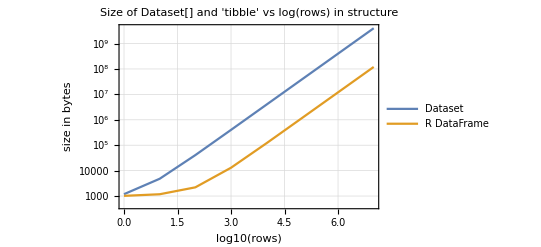

```mathematica
ListLogPlot[{InsertXs[mathSizes],InsertXs[rSizes]},
Joined->True,
PlotLegends->{"Dataset","R DataFrame"},
Frame->True,GridLines->Automatic,
PlotLabel->"Size of Dataset[] and 'tibble' vs log(rows) in structure",
FrameLabel->{"log10(rows)","size in bytes"}]
```

## Compare Size Ratios: w/ two columns, math dataset => 33x bigger

```mathematica
sizeRatios=MapThread[N[#1/#2]&,{mathSizes,rSizes}]
```

{1.16535,4.06803,18.5636,30.8418,33.0647,33.3063,33.3306,33.3331}

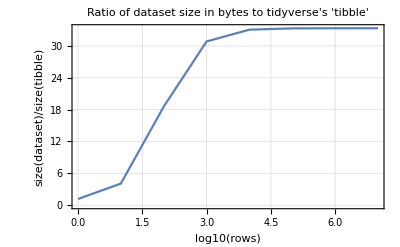

```mathematica
ListPlot[InsertXs[sizeRatios],
Frame->True,GridLines->Automatic,Joined->True,
PlotLabel->"Ratio of dataset size in bytes to tidyverse's 'tibble'",
FrameLabel->{"log10(rows)","size(dataset)/size(tibble)"}]
```

### Note: if table has more columns, ratio will increase even more since column names are repeated in Associations. Propose Wolfram creates DatasetColumnar[] and make all graphical and statistic functions talk directly with it (without the need to “peel” its internal contents)